```mathematica
a={8/10,6/10};
b=1;
u[x_,y_]:=1+Sin[π(1+x)(1+y)^2/8]
```

```mathematica
v=Table[{Cos[n π/(2.1 12)],Sin[n π/(2.1 12)]},{n,1,12}]
```

{{0.992239,0.124344},{0.969077,0.246757},{0.930874,0.365341},{0.878222,0.478254},{0.811938,0.583744},{0.733052,0.680173},{0.642788,0.766044},{0.542546,0.840026},{0.433884,0.900969},{0.318487,0.947927},{0.198146,0.980172},{0.0747301,0.997204}}

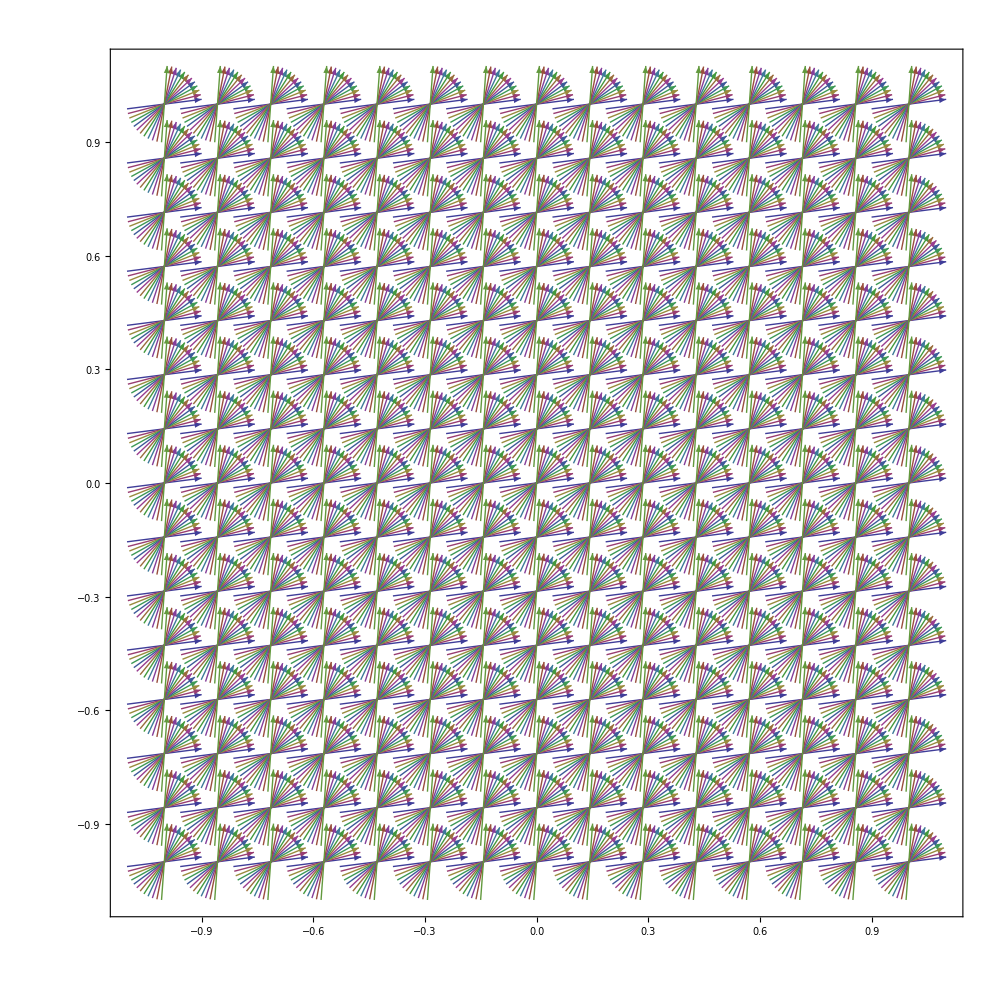

```mathematica
VectorPlot[v,{x,-1,1},{y,-1,1},VectorStyle->Arrowheads[0.01]]
```

```mathematica
Plot3D[u[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
f[x_,y_]:=a.{D[u[r,s],r],D[u[r,s],s]}+b u[r,s]/.{r->x,s->y}
```

```mathematica
f[x,y]
```

1+3/20 π (1+x) (1+y) Cos[1/8 π (1+x) (1+y)^2]+1/10 π (1+y)^2 Cos[1/8 π (1+x) (1+y)^2]+Sin[1/8 π (1+x) (1+y)^2]

```mathematica
CForm[%]
```

1 + (3*Pi*(1 + x)*(1 + y)*Cos((Pi*(1 + x)*Power(1 + y,2))/8.))/20. + (Pi*Power(1 + y,2)*Cos((Pi*(1 + x)*Power(1 + y,2))/8.))/10. + 
   Sin((Pi*(1 + x)*Power(1 + y,2))/8.)

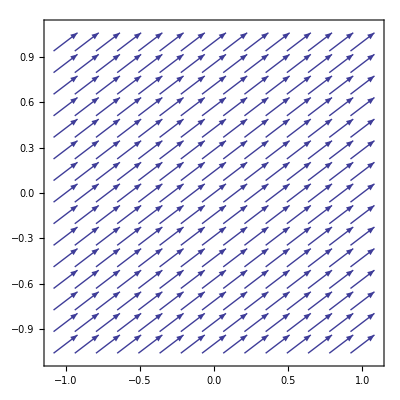

```mathematica
VectorPlot[a,{x,-1,1},{y,-1,1}]
```

```mathematica
Plot3D[f[x,y],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
u[x,-1]//FullSimplify
```

1

```mathematica
u[x,1]//FullSimplify
```

1+Cos[(π x)/2]

```mathematica
u[-1,y]//FullSimplify
```

1

```mathematica
u[1,y]//FullSimplify
```

1+Sin[1/4 π (1+y)^2]

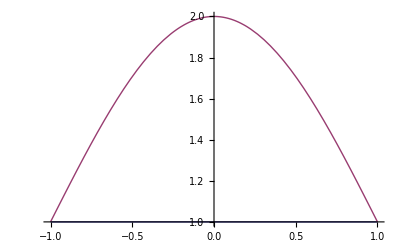

```mathematica
Plot[{u[x,-1],u[x,1]},{x,-1,1}]
```